```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

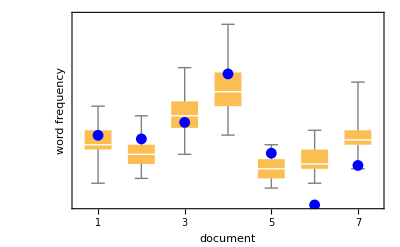

```mathematica
proportions = {10,7,15,20,4,6,11};
gFinal=Show[BoxWhiskerChart[RandomVariate[PoissonDistribution[#],{100}]&/@proportions,Frame->{True,True,False,False},FrameLabel->{"document","word frequency"},FrameTicks->{True,False},ChartLabels->Range@7,BaseStyle->{FontSize->14}],ListPlot[proportions+RandomVariate[NormalDistribution[0,5],{7}],PlotStyle->Blue]]
```

```mathematica
Export["Evaluation_wordPPC.pdf",gFinal]
```

Evaluation_wordPPC.pdf